```mathematica
<<X`
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

Suppose we have a real scalar field with interaction



Reality of the Lagrangian requires that we also have the term



In particular, the  is not conjugated due to the presence of the , since 

.

Note that if , the interaction Lagrangian becomes



which entails that in this scenario, the PC case must be pure-real, and the PV case must be pure-imaginary. However, there appears to be no such constraint in general. 

Note that this real scalar is a special case of a flavor-violating ALP. In particular, imagine an ALP with interaction

where  and  are complex. In this case, 



Using integration by parts, we have



We have often neglected the first term, although at least for , this term contributes to the ALP-photon vertex due to the chiral anomaly. Assuming , I don’t think this is a concern, although I’m not complete sure. We can then use the equations of motion, noting that  and . 



In particular, if we match to the real scalar with  and assume that V and  are real, it appears that  (to recover the factor of  out front),  (to recover the negative sign in front of the  term, as ),   and . 

 With this in mind, we can compute the contribution of this real scalar to the dipole moment of , and it should double as the contribution from the PV ALP. 
 
 We have three vertices.
 (1) Annihilating a , creating a  and a . This vertex corresponds to the Lagrangian term , and is given by . 
 (2) Annihilating a  and , and creating a . This vertex corresponds to the Lagrangian term , and is given by . 
 (3) Annihilating a  creating a  and a . This is the standard electromagnetic vertex with , where  is the electric charge.

```mathematica
VertexIJ =g*Exp[-I*ϕ]*(Cos[θ]𝟙+I*Exp[-I*δ]Sin[θ]γ5);
VertexJI= g*Exp[+I*ϕ]*(Cos[θ]𝟙+I*Exp[+I*δ]Sin[θ]γ5);
VertexEM=-e*Subscript[γ, μ];
```

We will call the incoming and outgoing momenta  and , with the photon momentum . With this, we have  and . We can include these simplifications in our calculation:

```mathematica
kinematics = {q1.q1->mi^2,q2.q2->mi^2,q1.q2->(mi^2+mi^2-q.q)/2,-q1+q2->q};
```

Let the internal momentum of the first  be . Then, the amplitude should be given by


We can get this into the form required by PackageX by “rationalizing” the denominators of the fermion propagators. Doing so yields

In this form, we can find the amplitude (there is a factor of  required for PackageX):

```mathematica
M=ReleaseHold[-1/(16 π^2)(LoopIntegrate[⟨𝓊[q2,mi],I*VertexJI,I*((k+q2-q1).γ+mj 𝟙),-I*e*Subscript[γ, μ],I*(k.γ+mj 𝟙),I*VertexIJ,𝓊[q1,mi]⟩,k,{-q1+k,mϕ},{q2-q1+k,mj},{k,mj}])/.kinematics//LoopRefine];
```

According to arXiv:0402058, the dipole moment can be parametrized in the following way:



However, if one also incorporates gauge invariance via , we find the relationship  This requires that   and . With this, the amplitude should be expressible in terms of four real form factors. Namely,

Which are the charge, magnetic dipole moment, electric dipole moment, and anapole moment respectively. Let us begin by finding the coefficients of the terms in the first expression. We have:

```mathematica
terms = {⟨𝓊[q2,mi],𝓊[q1,mi]⟩Subscript[q, μ],⟨𝓊[q2,mi],γ5,𝓊[q1,mi]⟩Subscript[q, μ],⟨𝓊[q2,mi],Subscript[γ, μ],𝓊[q1,mi]⟩,⟨𝓊[q2,mi],Subscript[γ, μ],γ5,𝓊[q1,mi]⟩,⟨𝓊[q2,mi],Subscript[σ, μ,{q}],𝓊[q1,mi]⟩ ,⟨𝓊[q2,mi],Subscript[σ, μ,{q}],γ5,𝓊[q1,mi]⟩ };
```

```mathematica
f1=Coefficient[M,terms[[1]]];
f2=Coefficient[M,terms[[2]]];
f3=Coefficient[M,terms[[3]]];
f4=Coefficient[M,terms[[4]]];
f5=Coefficient[M,terms[[5]]];
f6=Coefficient[M,terms[[6]]];
```

```mathematica
FullSimplify[f6]
```

(ⅈ e ⅇ^(-ⅈ δ) (1+ⅇ^(2 ⅈ δ)) g^2 mj (2 mi^2 DiscB[mi^2,mj,mϕ]-2 mi^2 DiscB[q.q,mj,mj]-(mi^2-mj^2+mϕ^2) (-Log[mj^2/mϕ^2]+2 mi^2 ScalarC0[mi^2,mi^2,q.q,mj,mϕ,mj])) Sin[2 θ])/(32 mi^2 π^2 (4 mi^2-q.q))

Note that  is zero, as required by gauge invariance.

```mathematica
f1
```

0

We should also find that . However, we have:

```mathematica
FullSimplify[f2*q.q+2mi*f4]
```

-(e ⅇ^(-ⅈ δ) (-1+ⅇ^(2 ⅈ δ)) g^2 ((2 mi^4)/ϵ+2 mi^2 (2 mi^2+mj^2-mϕ^2)+2 mi^2 (mi^2+mj^2-mϕ^2) DiscB[mi^2,mj,mϕ]+2 mi^4 Log[µ^2/mj^2]+(mi^4+2 mi^2 mϕ^2-(mj^2-mϕ^2)^2) Log[mj^2/mϕ^2]) Sin[2 θ])/(64 mi^3 π^2)

This is problematic, as it implies that gauge invariance is not satisfied. In particular, this is the case as long as , so it appears we can restore gauge invariance by setting  or  or  or . Focusing on the first scenario, this seems to imply that the real scalar Lagrangian must be parametrized by the interaction

.

I don’t see why this interaction term would have any relation to gauge invariance... If this is a problem, then it is also problematic for a PV-violating ALP, because one would expect , not 0 (at least in the case where  and are real).

Let us double-check that this is an issue by explicitly checking the Ward Identity on the amplitude:

```mathematica
qdotM=ReleaseHold[-1/(16 π^2)(Contract[Subscript[(q2-q1), μ] LoopIntegrate[⟨𝓊[q2,mi],I*VertexJI,I*((k+q2-q1).γ+mj 𝟙),-I*e*Subscript[γ, μ],I*(k.γ+mj 𝟙),I*VertexIJ,𝓊[q1,mi]⟩,k,{-q1+k,mϕ},{q2-q1+k,mj},{k,mj}]])/.kinematics//LoopRefine];
```

```mathematica
FullSimplify[qdotM]
```

-1/(64 mi^3 π^2)e ⅇ^(-ⅈ δ) (-1+ⅇ^(2 ⅈ δ)) g^2 ⟨𝓊[q2,mi],γ5,𝓊[q1,mi]⟩ ((2 mi^4)/ϵ+2 mi^2 (2 mi^2+mj^2-mϕ^2)+2 mi^2 (mi^2+mj^2-mϕ^2) DiscB[mi^2,mj,mϕ]+2 mi^4 Log[µ^2/mj^2]+(mi^4+2 mi^2 mϕ^2-(mj^2-mϕ^2)^2) Log[mj^2/mϕ^2]) Sin[2 θ]

Once again, this should be zero, but it isn’t. It is worth noting that the remaining term is proportional to , which is the axial vector current. This is reminiscent of anomalies to me, but I need a refresher...

```mathematica
1/T Integrate[1/l Exp[-(z-L/T t)/l],{t,0,T}]
```

(ⅇ^(-z/l) (-1+ⅇ^(L/l)))/L

```mathematica
1/T Integrate[1/l Exp[-(z-L/T t)/l],{z,0,L}]
```

(ⅇ^((L (t-T))/(l T)) (-1+ⅇ^(L/l)))/T

```mathematica
Assuming[{L>0,T>0},1/T Integrate[Integrate[DiracDelta[z-L/T t],{z,0,L}],{t,0,T}]]
```

1

```mathematica
Assuming[{L>0,T>0},FullSimplify[1/T Integrate[Integrate[1/l Exp[-(z-L/T t)/l],{z,L/T t,L}],{t,0,T}]]]
```

1+((-1+ⅇ^(-L/l)) l)/L

```mathematica
Normal[Series[1+((-1+ⅇ^(-L/l)) l)/L,{l,0,1}]]
```

1-l/L+(ⅇ^(-L/l) l)/L

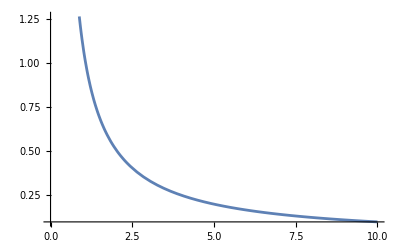

```mathematica
Plot[(2 l (-1+Cosh[L/l]))/L/.{L->1},{l,0,10}]
```

```mathematica
FullSimplify[Normal[Series[(ⅇ^(-L/l) (-1+ⅇ^(L/l)) (-1+ⅇ^(L/l)) l)/L,{l,0,1}]]]
```

(2 l (-1+Cosh[L/l]))/L

9.85035557009×10^433